```mathematica
values=With[
{step=100, base=10},
Table[
With[
{a=Timing[{exp,exp+step,AlgoList3[base^exp,base^(exp+step),{3,5,7,11}]}]},
Print[a];Last[Last[Last[a]]]],
{exp,0,67900,step}
]
]
```

{1.71383×10^-11,{0,100,{{3,5,7,11},{1,3160},921}}}

{1.71383×10^-11,{100,200,{{3,5,7,11},{},965}}}

{1.71383×10^-11,{200,300,{{3,5,7,11},{},941}}}

{1.71383×10^-11,{300,400,{{3,5,7,11},{},949}}}

{1.71383×10^-11,{400,500,{{3,5,7,11},{},1137}}}

{1.71383×10^-11,{500,600,{{3,5,7,11},{},1008}}}

{1.71383×10^-11,{600,700,{{3,5,7,11},{},1046}}}

{1.71383×10^-11,{700,800,{{3,5,7,11},{},995}}}

{1.71383×10^-11,{800,900,{{3,5,7,11},{},1045}}}

{1.71383×10^-11,{900,1000,{{3,5,7,11},{},1111}}}

{1.71383×10^-11,{1000,1100,{{3,5,7,11},{},1058}}}

{1.71383×10^-11,{1100,1200,{{3,5,7,11},{},893}}}

{1.71383×10^-11,{1200,1300,{{3,5,7,11},{},1129}}}

{1.71383×10^-11,{1300,1400,{{3,5,7,11},{},999}}}

{1.71383×10^-11,{1400,1500,{{3,5,7,11},{},1024}}}

{1.71383×10^-11,{1500,1600,{{3,5,7,11},{},1070}}}

{1.71383×10^-11,{1600,1700,{{3,5,7,11},{},1063}}}

{1.71383×10^-11,{1700,1800,{{3,5,7,11},{},967}}}

{1.71383×10^-11,{1800,1900,{{3,5,7,11},{},1028}}}

{1.71383×10^-11,{1900,2000,{{3,5,7,11},{},992}}}

{1.71383×10^-11,{2000,2100,{{3,5,7,11},{},907}}}

{1.71383×10^-11,{2100,2200,{{3,5,7,11},{},1018}}}

{1.71383×10^-11,{2200,2300,{{3,5,7,11},{},963}}}

{1.71383×10^-11,{2300,2400,{{3,5,7,11},{},905}}}

{1.71383×10^-11,{2400,2500,{{3,5,7,11},{},931}}}

{1.71383×10^-11,{2500,2600,{{3,5,7,11},{},888}}}

{1.71383×10^-11,{2600,2700,{{3,5,7,11},{},1024}}}

{1.71383×10^-11,{2700,2800,{{3,5,7,11},{},910}}}

{1.71383×10^-11,{2800,2900,{{3,5,7,11},{},1027}}}

{1.71383×10^-11,{2900,3000,{{3,5,7,11},{},887}}}

{1.71383×10^-11,{3000,3100,{{3,5,7,11},{},937}}}

{1.71383×10^-11,{3100,3200,{{3,5,7,11},{},965}}}

{1.71383×10^-11,{3200,3300,{{3,5,7,11},{},932}}}

{1.71383×10^-11,{3300,3400,{{3,5,7,11},{},928}}}

{1.71383×10^-11,{3400,3500,{{3,5,7,11},{},996}}}

{1.71383×10^-11,{3500,3600,{{3,5,7,11},{},922}}}

{1.71383×10^-11,{3600,3700,{{3,5,7,11},{},1004}}}

{1.71383×10^-11,{3700,3800,{{3,5,7,11},{},1049}}}

{1.71383×10^-11,{3800,3900,{{3,5,7,11},{},945}}}

{0.016,{3900,4000,{{3,5,7,11},{},1020}}}

{1.38698×10^-11,{4000,4100,{{3,5,7,11},{},933}}}

{1.38698×10^-11,{4100,4200,{{3,5,7,11},{},1068}}}

{1.38698×10^-11,{4200,4300,{{3,5,7,11},{},1081}}}

{1.38698×10^-11,{4300,4400,{{3,5,7,11},{},1001}}}

{1.38698×10^-11,{4400,4500,{{3,5,7,11},{},1029}}}

{1.38698×10^-11,{4500,4600,{{3,5,7,11},{},1002}}}

{1.38698×10^-11,{4600,4700,{{3,5,7,11},{},1024}}}

{1.38698×10^-11,{4700,4800,{{3,5,7,11},{},978}}}

{1.38698×10^-11,{4800,4900,{{3,5,7,11},{},982}}}

{1.38698×10^-11,{4900,5000,{{3,5,7,11},{},971}}}

{1.38698×10^-11,{5000,5100,{{3,5,7,11},{},845}}}

{1.38698×10^-11,{5100,5200,{{3,5,7,11},{},981}}}

{1.38698×10^-11,{5200,5300,{{3,5,7,11},{},1022}}}

{1.38698×10^-11,{5300,5400,{{3,5,7,11},{},949}}}

{1.38698×10^-11,{5400,5500,{{3,5,7,11},{},1099}}}

{1.38698×10^-11,{5500,5600,{{3,5,7,11},{},971}}}

{1.38698×10^-11,{5600,5700,{{3,5,7,11},{},966}}}

{1.38698×10^-11,{5700,5800,{{3,5,7,11},{},978}}}

{1.38698×10^-11,{5800,5900,{{3,5,7,11},{},928}}}

{1.38698×10^-11,{5900,6000,{{3,5,7,11},{},960}}}

{1.38698×10^-11,{6000,6100,{{3,5,7,11},{},931}}}

{1.38698×10^-11,{6100,6200,{{3,5,7,11},{},920}}}

{1.38698×10^-11,{6200,6300,{{3,5,7,11},{},955}}}

{1.38698×10^-11,{6300,6400,{{3,5,7,11},{},1033}}}

{0.015,{6400,6500,{{3,5,7,11},{},940}}}

{0.,{6500,6600,{{3,5,7,11},{},967}}}

{0.,{6600,6700,{{3,5,7,11},{},927}}}

{0.,{6700,6800,{{3,5,7,11},{},1022}}}

{0.,{6800,6900,{{3,5,7,11},{},1003}}}

{0.,{6900,7000,{{3,5,7,11},{},962}}}

{0.,{7000,7100,{{3,5,7,11},{},919}}}

{0.,{7100,7200,{{3,5,7,11},{},981}}}

{0.,{7200,7300,{{3,5,7,11},{},1019}}}

{0.,{7300,7400,{{3,5,7,11},{},956}}}

{0.,{7400,7500,{{3,5,7,11},{},935}}}

{0.,{7500,7600,{{3,5,7,11},{},983}}}

{0.,{7600,7700,{{3,5,7,11},{},994}}}

{0.,{7700,7800,{{3,5,7,11},{},1024}}}

{0.,{7800,7900,{{3,5,7,11},{},933}}}

{0.,{7900,8000,{{3,5,7,11},{},1021}}}

{0.,{8000,8100,{{3,5,7,11},{},1040}}}

{0.,{8100,8200,{{3,5,7,11},{},962}}}

{0.,{8200,8300,{{3,5,7,11},{},972}}}

{0.016,{8300,8400,{{3,5,7,11},{},1046}}}

{0.,{8400,8500,{{3,5,7,11},{},901}}}

{0.,{8500,8600,{{3,5,7,11},{},1013}}}

{0.,{8600,8700,{{3,5,7,11},{},940}}}

{0.,{8700,8800,{{3,5,7,11},{},904}}}

{0.,{8800,8900,{{3,5,7,11},{},951}}}

{0.,{8900,9000,{{3,5,7,11},{},1048}}}

{0.,{9000,9100,{{3,5,7,11},{},1007}}}

{0.,{9100,9200,{{3,5,7,11},{},1045}}}

{0.,{9200,9300,{{3,5,7,11},{},993}}}

{0.,{9300,9400,{{3,5,7,11},{},999}}}

{0.,{9400,9500,{{3,5,7,11},{},1107}}}

{0.,{9500,9600,{{3,5,7,11},{},947}}}

{0.,{9600,9700,{{3,5,7,11},{},984}}}

{0.015,{9700,9800,{{3,5,7,11},{},979}}}

{0.,{9800,9900,{{3,5,7,11},{},1059}}}

{0.,{9900,10000,{{3,5,7,11},{},1007}}}

{0.,{10000,10100,{{3,5,7,11},{},1069}}}

{0.,{10100,10200,{{3,5,7,11},{},980}}}

{0.,{10200,10300,{{3,5,7,11},{},1008}}}

{0.,{10300,10400,{{3,5,7,11},{},1000}}}

{0.,{10400,10500,{{3,5,7,11},{},1029}}}

{0.,{10500,10600,{{3,5,7,11},{},1062}}}

{0.,{10600,10700,{{3,5,7,11},{},980}}}

{0.,{10700,10800,{{3,5,7,11},{},947}}}

{0.,{10800,10900,{{3,5,7,11},{},972}}}

{0.,{10900,11000,{{3,5,7,11},{},987}}}

{0.,{11000,11100,{{3,5,7,11},{},990}}}

{0.,{11100,11200,{{3,5,7,11},{},939}}}

{0.,{11200,11300,{{3,5,7,11},{},1044}}}

{0.,{11300,11400,{{3,5,7,11},{},1026}}}

{0.,{11400,11500,{{3,5,7,11},{},946}}}

{0.,{11500,11600,{{3,5,7,11},{},1035}}}

{0.,{11600,11700,{{3,5,7,11},{},864}}}

{0.,{11700,11800,{{3,5,7,11},{},894}}}

{0.,{11800,11900,{{3,5,7,11},{},1064}}}

{0.,{11900,12000,{{3,5,7,11},{},1036}}}

{0.016,{12000,12100,{{3,5,7,11},{},1049}}}

{0.,{12100,12200,{{3,5,7,11},{},1041}}}

{0.,{12200,12300,{{3,5,7,11},{},945}}}

{0.,{12300,12400,{{3,5,7,11},{},962}}}

{0.,{12400,12500,{{3,5,7,11},{},941}}}

{0.,{12500,12600,{{3,5,7,11},{},1046}}}

{0.,{12600,12700,{{3,5,7,11},{},979}}}

{0.,{12700,12800,{{3,5,7,11},{},969}}}

{0.,{12800,12900,{{3,5,7,11},{},967}}}

{0.015,{12900,13000,{{3,5,7,11},{},967}}}

{2.03784×10^-11,{13000,13100,{{3,5,7,11},{},1014}}}

{2.03784×10^-11,{13100,13200,{{3,5,7,11},{},1021}}}

{2.03784×10^-11,{13200,13300,{{3,5,7,11},{},986}}}

{2.03784×10^-11,{13300,13400,{{3,5,7,11},{},1002}}}

{2.03784×10^-11,{13400,13500,{{3,5,7,11},{},914}}}

{2.03784×10^-11,{13500,13600,{{3,5,7,11},{},915}}}

{2.03784×10^-11,{13600,13700,{{3,5,7,11},{},974}}}

{2.03784×10^-11,{13700,13800,{{3,5,7,11},{},897}}}

{2.03784×10^-11,{13800,13900,{{3,5,7,11},{},978}}}

{1.71383×10^-11,{13900,14000,{{3,5,7,11},{},982}}}

{1.71383×10^-11,{14000,14100,{{3,5,7,11},{},1027}}}

{1.71383×10^-11,{14100,14200,{{3,5,7,11},{},1052}}}

{1.71383×10^-11,{14200,14300,{{3,5,7,11},{},1012}}}

{1.71383×10^-11,{14300,14400,{{3,5,7,11},{},901}}}

{1.71383×10^-11,{14400,14500,{{3,5,7,11},{},946}}}

{1.71383×10^-11,{14500,14600,{{3,5,7,11},{},968}}}

{1.71383×10^-11,{14600,14700,{{3,5,7,11},{},1046}}}

{1.71383×10^-11,{14700,14800,{{3,5,7,11},{},883}}}

{0.015,{14800,14900,{{3,5,7,11},{},971}}}

{3.15481×10^-12,{14900,15000,{{3,5,7,11},{},885}}}

{3.15481×10^-12,{15000,15100,{{3,5,7,11},{},961}}}

{3.15481×10^-12,{15100,15200,{{3,5,7,11},{},950}}}

{3.15481×10^-12,{15200,15300,{{3,5,7,11},{},1014}}}

{3.15481×10^-12,{15300,15400,{{3,5,7,11},{},944}}}

{3.15481×10^-12,{15400,15500,{{3,5,7,11},{},978}}}

{3.15481×10^-12,{15500,15600,{{3,5,7,11},{},904}}}

{0.016,{15600,15700,{{3,5,7,11},{},1020}}}

{0.,{15700,15800,{{3,5,7,11},{},952}}}

{0.,{15800,15900,{{3,5,7,11},{},1092}}}

{0.,{15900,16000,{{3,5,7,11},{},957}}}

{0.,{16000,16100,{{3,5,7,11},{},970}}}

{0.,{16100,16200,{{3,5,7,11},{},953}}}

{0.,{16200,16300,{{3,5,7,11},{},990}}}

{0.,{16300,16400,{{3,5,7,11},{},950}}}

{0.016,{16400,16500,{{3,5,7,11},{},970}}}

{0.,{16500,16600,{{3,5,7,11},{},859}}}

{0.,{16600,16700,{{3,5,7,11},{},1041}}}

{0.,{16700,16800,{{3,5,7,11},{},909}}}

{0.,{16800,16900,{{3,5,7,11},{},930}}}

{0.,{16900,17000,{{3,5,7,11},{},1003}}}

{0.015,{17000,17100,{{3,5,7,11},{},1038}}}

{0.,{17100,17200,{{3,5,7,11},{},914}}}

{0.,{17200,17300,{{3,5,7,11},{},1023}}}

{0.,{17300,17400,{{3,5,7,11},{},936}}}

{0.,{17400,17500,{{3,5,7,11},{},976}}}

{0.,{17500,17600,{{3,5,7,11},{},991}}}

{0.,{17600,17700,{{3,5,7,11},{},945}}}

{0.016,{17700,17800,{{3,5,7,11},{},959}}}

{0.,{17800,17900,{{3,5,7,11},{},936}}}

{0.,{17900,18000,{{3,5,7,11},{},1015}}}

{0.,{18000,18100,{{3,5,7,11},{},936}}}

{0.,{18100,18200,{{3,5,7,11},{},995}}}

{0.015,{18200,18300,{{3,5,7,11},{},942}}}

{2.36469×10^-11,{18300,18400,{{3,5,7,11},{},923}}}

{2.36469×10^-11,{18400,18500,{{3,5,7,11},{},933}}}

{2.36469×10^-11,{18500,18600,{{3,5,7,11},{},984}}}

{2.36469×10^-11,{18600,18700,{{3,5,7,11},{},992}}}

{2.36469×10^-11,{18700,18800,{{3,5,7,11},{},980}}}

{2.36469×10^-11,{18800,18900,{{3,5,7,11},{},1100}}}

{0.016,{18900,19000,{{3,5,7,11},{},978}}}

{2.03784×10^-11,{19000,19100,{{3,5,7,11},{},1105}}}

{2.03784×10^-11,{19100,19200,{{3,5,7,11},{},1022}}}

{2.03784×10^-11,{19200,19300,{{3,5,7,11},{},1046}}}

{2.03784×10^-11,{19300,19400,{{3,5,7,11},{},979}}}

{2.03784×10^-11,{19400,19500,{{3,5,7,11},{},1083}}}

{2.03784×10^-11,{19500,19600,{{3,5,7,11},{},970}}}

{0.016,{19600,19700,{{3,5,7,11},{},994}}}

{1.71383×10^-11,{19700,19800,{{3,5,7,11},{},1083}}}

{1.71383×10^-11,{19800,19900,{{3,5,7,11},{},932}}}

{1.71383×10^-11,{19900,20000,{{3,5,7,11},{},1077}}}

{1.71383×10^-11,{20000,20100,{{3,5,7,11},{},1041}}}

{0.015,{20100,20200,{{3,5,7,11},{},845}}}

{3.15481×10^-12,{20200,20300,{{3,5,7,11},{},1112}}}

{3.15481×10^-12,{20300,20400,{{3,5,7,11},{},1009}}}

{3.15481×10^-12,{20400,20500,{{3,5,7,11},{},986}}}

{3.15481×10^-12,{20500,20600,{{3,5,7,11},{},1108}}}

{3.15481×10^-12,{20600,20700,{{3,5,7,11},{},969}}}

{0.,{20700,20800,{{3,5,7,11},{},949}}}

{0.,{20800,20900,{{3,5,7,11},{},1077}}}

{0.,{20900,21000,{{3,5,7,11},{},1052}}}

{0.,{21000,21100,{{3,5,7,11},{},941}}}

{0.,{21100,21200,{{3,5,7,11},{},961}}}

{0.015,{21200,21300,{{3,5,7,11},{},929}}}

{0.,{21300,21400,{{3,5,7,11},{},1005}}}

{0.,{21400,21500,{{3,5,7,11},{},949}}}

{0.,{21500,21600,{{3,5,7,11},{},935}}}

{0.,{21600,21700,{{3,5,7,11},{},983}}}

{0.016,{21700,21800,{{3,5,7,11},{},1086}}}

{0.,{21800,21900,{{3,5,7,11},{},918}}}

{0.,{21900,22000,{{3,5,7,11},{},940}}}

{0.,{22000,22100,{{3,5,7,11},{},951}}}

{0.,{22100,22200,{{3,5,7,11},{},1119}}}

{0.016,{22200,22300,{{3,5,7,11},{},977}}}

{0.,{22300,22400,{{3,5,7,11},{},1034}}}

{0.,{22400,22500,{{3,5,7,11},{},965}}}

{0.,{22500,22600,{{3,5,7,11},{},949}}}

{0.015,{22600,22700,{{3,5,7,11},{},1083}}}

{2.36469×10^-11,{22700,22800,{{3,5,7,11},{},1048}}}

{2.36469×10^-11,{22800,22900,{{3,5,7,11},{},979}}}

{2.36469×10^-11,{22900,23000,{{3,5,7,11},{},1119}}}

{2.36469×10^-11,{23000,23100,{{3,5,7,11},{},943}}}

{0.016,{23100,23200,{{3,5,7,11},{},892}}}

{2.03784×10^-11,{23200,23300,{{3,5,7,11},{},867}}}

{2.03784×10^-11,{23300,23400,{{3,5,7,11},{},1050}}}

{2.03784×10^-11,{23400,23500,{{3,5,7,11},{},800}}}

{0.015,{23500,23600,{{3,5,7,11},{},1003}}}

{6.42331×10^-12,{23600,23700,{{3,5,7,11},{},1036}}}

{6.42331×10^-12,{23700,23800,{{3,5,7,11},{},970}}}

{6.42331×10^-12,{23800,23900,{{3,5,7,11},{},1002}}}

{6.42331×10^-12,{23900,24000,{{3,5,7,11},{},960}}}

{0.016,{24000,24100,{{3,5,7,11},{},865}}}

{3.15481×10^-12,{24100,24200,{{3,5,7,11},{},1082}}}

{3.15481×10^-12,{24200,24300,{{3,5,7,11},{},949}}}

{3.15481×10^-12,{24300,24400,{{3,5,7,11},{},908}}}

{3.15481×10^-12,{24400,24500,{{3,5,7,11},{},949}}}

{0.016,{24500,24600,{{3,5,7,11},{},1057}}}

{0.,{24600,24700,{{3,5,7,11},{},976}}}

{0.,{24700,24800,{{3,5,7,11},{},1087}}}

{0.,{24800,24900,{{3,5,7,11},{},975}}}

{0.015,{24900,25000,{{3,5,7,11},{},961}}}

{0.,{25000,25100,{{3,5,7,11},{},905}}}

{0.,{25100,25200,{{3,5,7,11},{},1155}}}

{0.,{25200,25300,{{3,5,7,11},{},991}}}

{0.016,{25300,25400,{{3,5,7,11},{},951}}}

{0.,{25400,25500,{{3,5,7,11},{},1071}}}

{0.,{25500,25600,{{3,5,7,11},{},1026}}}

{0.,{25600,25700,{{3,5,7,11},{},967}}}

{0.015,{25700,25800,{{3,5,7,11},{},1001}}}

{2.69154×10^-11,{25800,25900,{{3,5,7,11},{},893}}}

{2.69154×10^-11,{25900,26000,{{3,5,7,11},{},1060}}}

{2.69154×10^-11,{26000,26100,{{3,5,7,11},{},925}}}

{0.016,{26100,26200,{{3,5,7,11},{},976}}}

{2.36469×10^-11,{26200,26300,{{3,5,7,11},{},954}}}

{2.36469×10^-11,{26300,26400,{{3,5,7,11},{},964}}}

{2.36469×10^-11,{26400,26500,{{3,5,7,11},{},991}}}

{0.016,{26500,26600,{{3,5,7,11},{},948}}}

{2.03784×10^-11,{26600,26700,{{3,5,7,11},{},926}}}

{2.03784×10^-11,{26700,26800,{{3,5,7,11},{},949}}}

{0.015,{26800,26900,{{3,5,7,11},{},933}}}

{6.42331×10^-12,{26900,27000,{{3,5,7,11},{},909}}}

{6.42331×10^-12,{27000,27100,{{3,5,7,11},{},838}}}

{6.42331×10^-12,{27100,27200,{{3,5,7,11},{},1026}}}

{0.016,{27200,27300,{{3,5,7,11},{},942}}}

{3.15481×10^-12,{27300,27400,{{3,5,7,11},{},916}}}

{3.15481×10^-12,{27400,27500,{{3,5,7,11},{},922}}}

{0.015,{27500,27600,{{3,5,7,11},{},989}}}

{0.,{27600,27700,{{3,5,7,11},{},911}}}

{0.,{27700,27800,{{3,5,7,11},{},1075}}}

{0.,{27800,27900,{{3,5,7,11},{},1072}}}

{0.016,{27900,28000,{{3,5,7,11},{},925}}}

{0.,{28000,28100,{{3,5,7,11},{},935}}}

{0.,{28100,28200,{{3,5,7,11},{},936}}}

{0.016,{28200,28300,{{3,5,7,11},{},925}}}

{0.,{28300,28400,{{3,5,7,11},{},944}}}

{0.,{28400,28500,{{3,5,7,11},{},969}}}

{0.,{28500,28600,{{3,5,7,11},{},944}}}

{0.015,{28600,28700,{{3,5,7,11},{},1027}}}

{2.69154×10^-11,{28700,28800,{{3,5,7,11},{},1035}}}

{2.69154×10^-11,{28800,28900,{{3,5,7,11},{},969}}}

{0.016,{28900,29000,{{3,5,7,11},{},965}}}

{2.36469×10^-11,{29000,29100,{{3,5,7,11},{},936}}}

{2.36469×10^-11,{29100,29200,{{3,5,7,11},{},1004}}}

{0.015,{29200,29300,{{3,5,7,11},{},1021}}}

{9.66338×10^-12,{29300,29400,{{3,5,7,11},{},909}}}

{9.66338×10^-12,{29400,29500,{{3,5,7,11},{},1016}}}

{9.66338×10^-12,{29500,29600,{{3,5,7,11},{},983}}}

{0.016,{29600,29700,{{3,5,7,11},{},994}}}

{6.42331×10^-12,{29700,29800,{{3,5,7,11},{},915}}}

{6.42331×10^-12,{29800,29900,{{3,5,7,11},{},1033}}}

{0.016,{29900,30000,{{3,5,7,11},{},853}}}

{3.15481×10^-12,{30000,30100,{{3,5,7,11},{},951}}}

{3.15481×10^-12,{30100,30200,{{3,5,7,11},{},906}}}

{3.15481×10^-12,{30200,30300,{{3,5,7,11},{},1001}}}

{0.015,{30300,30400,{{3,5,7,11},{},926}}}

{0.,{30400,30500,{{3,5,7,11},{},1023}}}

{0.,{30500,30600,{{3,5,7,11},{},1037}}}

{0.016,{30600,30700,{{3,5,7,11},{},1005}}}

{0.,{30700,30800,{{3,5,7,11},{},971}}}

{0.,{30800,30900,{{3,5,7,11},{},1046}}}

{0.015,{30900,31000,{{3,5,7,11},{},982}}}

{0.,{31000,31100,{{3,5,7,11},{},917}}}

{0.,{31100,31200,{{3,5,7,11},{},1014}}}

{0.016,{31200,31300,{{3,5,7,11},{},965}}}

{2.69154×10^-11,{31300,31400,{{3,5,7,11},{},956}}}

{2.69154×10^-11,{31400,31500,{{3,5,7,11},{},1034}}}

{0.016,{31500,31600,{{3,5,7,11},{},948}}}

{2.36469×10^-11,{31600,31700,{{3,5,7,11},{},1000}}}

{2.36469×10^-11,{31700,31800,{{3,5,7,11},{},998}}}

{0.015,{31800,31900,{{3,5,7,11},{},1057}}}

{9.66338×10^-12,{31900,32000,{{3,5,7,11},{},870}}}

{9.66338×10^-12,{32000,32100,{{3,5,7,11},{},956}}}

{0.016,{32100,32200,{{3,5,7,11},{},966}}}

{6.42331×10^-12,{32200,32300,{{3,5,7,11},{},1034}}}

{0.015,{32300,32400,{{3,5,7,11},{},1020}}}

{0.,{32400,32500,{{3,5,7,11},{},966}}}

{0.,{32500,32600,{{3,5,7,11},{},867}}}

{0.016,{32600,32700,{{3,5,7,11},{},1026}}}

{0.,{32700,32800,{{3,5,7,11},{},901}}}

{0.,{32800,32900,{{3,5,7,11},{},951}}}

{0.016,{32900,33000,{{3,5,7,11},{},907}}}

{0.,{33000,33100,{{3,5,7,11},{},953}}}

{0.,{33100,33200,{{3,5,7,11},{},931}}}

{0.015,{33200,33300,{{3,5,7,11},{},938}}}

{0.,{33300,33400,{{3,5,7,11},{},922}}}

{0.016,{33400,33500,{{3,5,7,11},{},948}}}

{2.69154×10^-11,{33500,33600,{{3,5,7,11},{},985}}}

{2.69154×10^-11,{33600,33700,{{3,5,7,11},{},955}}}

{0.015,{33700,33800,{{3,5,7,11},{},949}}}

{1.29319×10^-11,{33800,33900,{{3,5,7,11},{},1170}}}

{1.29319×10^-11,{33900,34000,{{3,5,7,11},{},991}}}

{1.29319×10^-11,{34000,34100,{{3,5,7,11},{},977}}}

{9.66338×10^-12,{34100,34200,{{3,5,7,11},{},914}}}

{9.66338×10^-12,{34200,34300,{{3,5,7,11},{},1060}}}

{9.66338×10^-12,{34300,34400,{{3,5,7,11},{},961}}}

{0.016,{34400,34500,{{3,5,7,11},{},1134}}}

{6.42331×10^-12,{34500,34600,{{3,5,7,11},{},910}}}

{6.42331×10^-12,{34600,34700,{{3,5,7,11},{},975}}}

{0.015,{34700,34800,{{3,5,7,11},{},915}}}

{0.,{34800,34900,{{3,5,7,11},{},920}}}

{0.016,{34900,35000,{{3,5,7,11},{},948}}}

{0.,{35000,35100,{{3,5,7,11},{},1022}}}

{0.,{35100,35200,{{3,5,7,11},{},933}}}

{0.015,{35200,35300,{{3,5,7,11},{},946}}}

{0.,{35300,35400,{{3,5,7,11},{},948}}}

{0.016,{35400,35500,{{3,5,7,11},{},948}}}

{0.,{35500,35600,{{3,5,7,11},{},918}}}

{0.,{35600,35700,{{3,5,7,11},{},1079}}}

{0.016,{35700,35800,{{3,5,7,11},{},947}}}

{2.69154×10^-11,{35800,35900,{{3,5,7,11},{},975}}}

{0.015,{35900,36000,{{3,5,7,11},{},910}}}

{1.29319×10^-11,{36000,36100,{{3,5,7,11},{},931}}}

{1.29319×10^-11,{36100,36200,{{3,5,7,11},{},944}}}

{0.016,{36200,36300,{{3,5,7,11},{},984}}}

{9.66338×10^-12,{36300,36400,{{3,5,7,11},{},983}}}

{0.015,{36400,36500,{{3,5,7,11},{},887}}}

{0.,{36500,36600,{{3,5,7,11},{},1018}}}

{0.,{36600,36700,{{3,5,7,11},{},1062}}}

{0.016,{36700,36800,{{3,5,7,11},{},932}}}

{0.,{36800,36900,{{3,5,7,11},{},1117}}}

{0.,{36900,37000,{{3,5,7,11},{},1106}}}

{0.016,{37000,37100,{{3,5,7,11},{},1006}}}

{0.,{37100,37200,{{3,5,7,11},{},1034}}}

{0.015,{37200,37300,{{3,5,7,11},{},938}}}

{0.,{37300,37400,{{3,5,7,11},{},961}}}

{0.016,{37400,37500,{{3,5,7,11},{},992}}}

{0.,{37500,37600,{{3,5,7,11},{},972}}}

{0.,{37600,37700,{{3,5,7,11},{},1009}}}

{0.015,{37700,37800,{{3,5,7,11},{},919}}}

{1.62004×10^-11,{37800,37900,{{3,5,7,11},{},932}}}

{0.016,{37900,38000,{{3,5,7,11},{},987}}}

{1.29319×10^-11,{38000,38100,{{3,5,7,11},{},963}}}

{0.016,{38100,38200,{{3,5,7,11},{},1074}}}

{9.66338×10^-12,{38200,38300,{{3,5,7,11},{},939}}}

{0.015,{38300,38400,{{3,5,7,11},{},994}}}

{0.,{38400,38500,{{3,5,7,11},{},1063}}}

{0.,{38500,38600,{{3,5,7,11},{},1083}}}

{0.016,{38600,38700,{{3,5,7,11},{},914}}}

{0.,{38700,38800,{{3,5,7,11},{},954}}}

{0.,{38800,38900,{{3,5,7,11},{},997}}}

{0.015,{38900,39000,{{3,5,7,11},{},934}}}

{0.,{39000,39100,{{3,5,7,11},{},957}}}

{0.,{39100,39200,{{3,5,7,11},{},934}}}

{0.,{39200,39300,{{3,5,7,11},{},935}}}

{0.,{39300,39400,{{3,5,7,11},{},1007}}}

{0.016,{39400,39500,{{3,5,7,11},{},946}}}

{0.,{39500,39600,{{3,5,7,11},{},995}}}

{0.015,{39600,39700,{{3,5,7,11},{},874}}}

{1.62004×10^-11,{39700,39800,{{3,5,7,11},{},885}}}

{0.016,{39800,39900,{{3,5,7,11},{},908}}}

{1.29319×10^-11,{39900,40000,{{3,5,7,11},{},1004}}}

{0.015,{40000,40100,{{3,5,7,11},{},1002}}}

{0.,{40100,40200,{{3,5,7,11},{},1077}}}

{0.016,{40200,40300,{{3,5,7,11},{},863}}}

{0.,{40300,40400,{{3,5,7,11},{},992}}}

{0.016,{40400,40500,{{3,5,7,11},{},980}}}

{0.,{40500,40600,{{3,5,7,11},{},915}}}

{0.015,{40600,40700,{{3,5,7,11},{},1003}}}

{0.016,{40700,40800,{{3,5,7,11},{},965}}}

{0.,{40800,40900,{{3,5,7,11},{},1068}}}

{0.015,{40900,41000,{{3,5,7,11},{},1125}}}

{1.94689×10^-11,{41000,41100,{{3,5,7,11},{},1002}}}

{0.016,{41100,41200,{{3,5,7,11},{},1132}}}

{1.62004×10^-11,{41200,41300,{{3,5,7,11},{},931}}}

{0.016,{41300,41400,{{3,5,7,11},{},1098}}}

{1.29319×10^-11,{41400,41500,{{3,5,7,11},{},947}}}

{0.015,{41500,41600,{{3,5,7,11},{},906}}}

{0.,{41600,41700,{{3,5,7,11},{},911}}}

{0.016,{41700,41800,{{3,5,7,11},{},1012}}}

{0.,{41800,41900,{{3,5,7,11},{},882}}}

{0.015,{41900,42000,{{3,5,7,11},{},999}}}

{0.,{42000,42100,{{3,5,7,11},{},1072}}}

{0.016,{42100,42200,{{3,5,7,11},{},1026}}}

{0.,{42200,42300,{{3,5,7,11},{},1071}}}

{0.016,{42300,42400,{{3,5,7,11},{},920}}}

{0.,{42400,42500,{{3,5,7,11},{},1072}}}

{0.015,{42500,42600,{{3,5,7,11},{},979}}}

{0.016,{42600,42700,{{3,5,7,11},{},988}}}

{1.62004×10^-11,{42700,42800,{{3,5,7,11},{},929}}}

{0.015,{42800,42900,{{3,5,7,11},{},1038}}}

{2.21689×10^-12,{42900,43000,{{3,5,7,11},{},992}}}

{0.016,{43000,43100,{{3,5,7,11},{},1007}}}

{0.,{43100,43200,{{3,5,7,11},{},1083}}}

{0.016,{43200,43300,{{3,5,7,11},{},1000}}}

{0.,{43300,43400,{{3,5,7,11},{},959}}}

{0.015,{43400,43500,{{3,5,7,11},{},955}}}

{0.,{43500,43600,{{3,5,7,11},{},950}}}

{0.016,{43600,43700,{{3,5,7,11},{},1047}}}

{0.015,{43700,43800,{{3,5,7,11},{},1023}}}

{2.27089×10^-11,{43800,43900,{{3,5,7,11},{},1047}}}

{0.016,{43900,44000,{{3,5,7,11},{},958}}}

{1.94689×10^-11,{44000,44100,{{3,5,7,11},{},1069}}}

{0.016,{44100,44200,{{3,5,7,11},{},1062}}}

{1.62004×10^-11,{44200,44300,{{3,5,7,11},{},942}}}

{0.015,{44300,44400,{{3,5,7,11},{},957}}}

{2.21689×10^-12,{44400,44500,{{3,5,7,11},{},1025}}}

{0.016,{44500,44600,{{3,5,7,11},{},1031}}}

{0.,{44600,44700,{{3,5,7,11},{},952}}}

{0.015,{44700,44800,{{3,5,7,11},{},1011}}}

{0.,{44800,44900,{{3,5,7,11},{},1005}}}

{0.016,{44900,45000,{{3,5,7,11},{},1035}}}

{0.,{45000,45100,{{3,5,7,11},{},1130}}}

{0.016,{45100,45200,{{3,5,7,11},{},1024}}}

{0.015,{45200,45300,{{3,5,7,11},{},992}}}

{2.27089×10^-11,{45300,45400,{{3,5,7,11},{},1041}}}

{0.016,{45400,45500,{{3,5,7,11},{},915}}}

{1.94689×10^-11,{45500,45600,{{3,5,7,11},{},967}}}

{0.015,{45600,45700,{{3,5,7,11},{},936}}}

{5.48539×10^-12,{45700,45800,{{3,5,7,11},{},863}}}

{0.016,{45800,45900,{{3,5,7,11},{},994}}}

{2.21689×10^-12,{45900,46000,{{3,5,7,11},{},925}}}

{0.016,{46000,46100,{{3,5,7,11},{},1031}}}

{0.,{46100,46200,{{3,5,7,11},{},972}}}

{0.015,{46200,46300,{{3,5,7,11},{},1059}}}

{0.,{46300,46400,{{3,5,7,11},{},861}}}

{0.016,{46400,46500,{{3,5,7,11},{},1135}}}

{0.015,{46500,46600,{{3,5,7,11},{},1033}}}

{2.59774×10^-11,{46600,46700,{{3,5,7,11},{},1021}}}

{0.016,{46700,46800,{{3,5,7,11},{},998}}}

{2.27089×10^-11,{46800,46900,{{3,5,7,11},{},1056}}}

{0.016,{46900,47000,{{3,5,7,11},{},892}}}

{1.94689×10^-11,{47000,47100,{{3,5,7,11},{},986}}}

{0.015,{47100,47200,{{3,5,7,11},{},955}}}

{5.48539×10^-12,{47200,47300,{{3,5,7,11},{},992}}}

{0.016,{47300,47400,{{3,5,7,11},{},952}}}

{0.015,{47400,47500,{{3,5,7,11},{},971}}}

{0.,{47500,47600,{{3,5,7,11},{},937}}}

{0.016,{47600,47700,{{3,5,7,11},{},1088}}}

{0.,{47700,47800,{{3,5,7,11},{},1069}}}

{0.016,{47800,47900,{{3,5,7,11},{},1072}}}

{0.015,{47900,48000,{{3,5,7,11},{},1005}}}

{2.59774×10^-11,{48000,48100,{{3,5,7,11},{},1029}}}

{0.016,{48100,48200,{{3,5,7,11},{},843}}}

{0.015,{48200,48300,{{3,5,7,11},{},937}}}

{8.75389×10^-12,{48300,48400,{{3,5,7,11},{},989}}}

{0.016,{48400,48500,{{3,5,7,11},{},1038}}}

{5.48539×10^-12,{48500,48600,{{3,5,7,11},{},962}}}

{0.016,{48600,48700,{{3,5,7,11},{},1041}}}

{2.21689×10^-12,{48700,48800,{{3,5,7,11},{},910}}}

{0.015,{48800,48900,{{3,5,7,11},{},1041}}}

{0.,{48900,49000,{{3,5,7,11},{},981}}}

{0.016,{49000,49100,{{3,5,7,11},{},947}}}

{0.015,{49100,49200,{{3,5,7,11},{},965}}}

{0.,{49200,49300,{{3,5,7,11},{},971}}}

{0.016,{49300,49400,{{3,5,7,11},{},958}}}

{2.59774×10^-11,{49400,49500,{{3,5,7,11},{},861}}}

{0.016,{49500,49600,{{3,5,7,11},{},1070}}}

{0.015,{49600,49700,{{3,5,7,11},{},1034}}}

{8.75389×10^-12,{49700,49800,{{3,5,7,11},{},944}}}

{0.016,{49800,49900,{{3,5,7,11},{},1171}}}

{5.48539×10^-12,{49900,50000,{{3,5,7,11},{},987}}}

{0.015,{50000,50100,{{3,5,7,11},{},970}}}

{0.016,{50100,50200,{{3,5,7,11},{},1002}}}

{0.,{50200,50300,{{3,5,7,11},{},946}}}

{0.016,{50300,50400,{{3,5,7,11},{},945}}}

{0.,{50400,50500,{{3,5,7,11},{},928}}}

{0.015,{50500,50600,{{3,5,7,11},{},993}}}

{0.016,{50600,50700,{{3,5,7,11},{},879}}}

{2.59774×10^-11,{50700,50800,{{3,5,7,11},{},1017}}}

{0.015,{50800,50900,{{3,5,7,11},{},1018}}}

{1.1994×10^-11,{50900,51000,{{3,5,7,11},{},944}}}

{0.016,{51000,51100,{{3,5,7,11},{},943}}}

{8.75389×10^-12,{51100,51200,{{3,5,7,11},{},948}}}

{0.016,{51200,51300,{{3,5,7,11},{},940}}}

{0.015,{51300,51400,{{3,5,7,11},{},951}}}

{0.,{51400,51500,{{3,5,7,11},{},846}}}

{0.016,{51500,51600,{{3,5,7,11},{},1008}}}

{0.,{51600,51700,{{3,5,7,11},{},923}}}

{0.015,{51700,51800,{{3,5,7,11},{},964}}}

{0.,{51800,51900,{{3,5,7,11},{},1045}}}

{0.016,{51900,52000,{{3,5,7,11},{},944}}}

{0.016,{52000,52100,{{3,5,7,11},{},1013}}}

{2.59774×10^-11,{52100,52200,{{3,5,7,11},{},975}}}

{0.015,{52200,52300,{{3,5,7,11},{},886}}}

{0.016,{52300,52400,{{3,5,7,11},{},906}}}

{8.75389×10^-12,{52400,52500,{{3,5,7,11},{},913}}}

{0.015,{52500,52600,{{3,5,7,11},{},910}}}

{0.016,{52600,52700,{{3,5,7,11},{},952}}}

{0.,{52700,52800,{{3,5,7,11},{},935}}}

{0.016,{52800,52900,{{3,5,7,11},{},998}}}

{0.015,{52900,53000,{{3,5,7,11},{},999}}}

{0.,{53000,53100,{{3,5,7,11},{},986}}}

{0.016,{53100,53200,{{3,5,7,11},{},1065}}}

{0.015,{53200,53300,{{3,5,7,11},{},912}}}

{1.52625×10^-11,{53300,53400,{{3,5,7,11},{},1088}}}

{0.016,{53400,53500,{{3,5,7,11},{},978}}}

{0.016,{53500,53600,{{3,5,7,11},{},896}}}

{8.75389×10^-12,{53600,53700,{{3,5,7,11},{},919}}}

{0.015,{53700,53800,{{3,5,7,11},{},995}}}

{0.016,{53800,53900,{{3,5,7,11},{},951}}}

{0.,{53900,54000,{{3,5,7,11},{},1089}}}

{0.015,{54000,54100,{{3,5,7,11},{},916}}}

{0.016,{54100,54200,{{3,5,7,11},{},950}}}

{0.016,{54200,54300,{{3,5,7,11},{},891}}}

{0.,{54300,54400,{{3,5,7,11},{},957}}}

{0.015,{54400,54500,{{3,5,7,11},{},1057}}}

{0.016,{54500,54600,{{3,5,7,11},{},958}}}

{0.015,{54600,54700,{{3,5,7,11},{},974}}}

{0.,{54700,54800,{{3,5,7,11},{},954}}}

{0.,{54800,54900,{{3,5,7,11},{},993}}}

{0.016,{54900,55000,{{3,5,7,11},{},1078}}}

{0.015,{55000,55100,{{3,5,7,11},{},995}}}

{0.,{55100,55200,{{3,5,7,11},{},982}}}

{0.016,{55200,55300,{{3,5,7,11},{},943}}}

{0.015,{55300,55400,{{3,5,7,11},{},1036}}}

{1.8531×10^-11,{55400,55500,{{3,5,7,11},{},930}}}

{0.016,{55500,55600,{{3,5,7,11},{},1218}}}

{0.016,{55600,55700,{{3,5,7,11},{},978}}}

{0.015,{55700,55800,{{3,5,7,11},{},1041}}}

{0.,{55800,55900,{{3,5,7,11},{},997}}}

{0.016,{55900,56000,{{3,5,7,11},{},935}}}

{0.015,{56000,56100,{{3,5,7,11},{},1030}}}

{0.016,{56100,56200,{{3,5,7,11},{},976}}}

{0.,{56200,56300,{{3,5,7,11},{},989}}}

{0.016,{56300,56400,{{3,5,7,11},{},1102}}}

{0.015,{56400,56500,{{3,5,7,11},{},1005}}}

{0.016,{56500,56600,{{3,5,7,11},{},1083}}}

{1.52625×10^-11,{56600,56700,{{3,5,7,11},{},1010}}}

{0.015,{56700,56800,{{3,5,7,11},{},962}}}

{0.016,{56800,56900,{{3,5,7,11},{},910}}}

{0.,{56900,57000,{{3,5,7,11},{},1061}}}

{0.016,{57000,57100,{{3,5,7,11},{},936}}}

{0.015,{57100,57200,{{3,5,7,11},{},1029}}}

{0.016,{57200,57300,{{3,5,7,11},{},952}}}

{0.015,{57300,57400,{{3,5,7,11},{},1039}}}

{0.016,{57400,57500,{{3,5,7,11},{},904}}}

{1.8531×10^-11,{57500,57600,{{3,5,7,11},{},1209}}}

{0.016,{57600,57700,{{3,5,7,11},{},922}}}

{0.015,{57700,57800,{{3,5,7,11},{},1016}}}

{0.016,{57800,57900,{{3,5,7,11},{},887}}}

{0.,{57900,58000,{{3,5,7,11},{},1083}}}

{0.015,{58000,58100,{{3,5,7,11},{},1010}}}

{0.016,{58100,58200,{{3,5,7,11},{},1016}}}

{0.016,{58200,58300,{{3,5,7,11},{},1032}}}

{0.,{58300,58400,{{3,5,7,11},{},1108}}}

{0.015,{58400,58500,{{3,5,7,11},{},967}}}

{0.016,{58500,58600,{{3,5,7,11},{},1031}}}

{1.8531×10^-11,{58600,58700,{{3,5,7,11},{},996}}}

{0.015,{58700,58800,{{3,5,7,11},{},975}}}

{0.016,{58800,58900,{{3,5,7,11},{},947}}}

{0.016,{58900,59000,{{3,5,7,11},{},948}}}

{0.015,{59000,59100,{{3,5,7,11},{},947}}}

{0.016,{59100,59200,{{3,5,7,11},{},973}}}

{0.,{59200,59300,{{3,5,7,11},{},957}}}

{0.015,{59300,59400,{{3,5,7,11},{},987}}}

{0.016,{59400,59500,{{3,5,7,11},{},987}}}

{0.016,{59500,59600,{{3,5,7,11},{},969}}}

{0.015,{59600,59700,{{3,5,7,11},{},1027}}}

{4.54747×10^-12,{59700,59800,{{3,5,7,11},{},1028}}}

{0.016,{59800,59900,{{3,5,7,11},{},1019}}}

{0.015,{59900,60000,{{3,5,7,11},{},923}}}

{0.016,{60000,60100,{{3,5,7,11},{},1057}}}

{0.016,{60100,60200,{{3,5,7,11},{},936}}}

{0.015,{60200,60300,{{3,5,7,11},{},921}}}

{2.50395×10^-11,{60300,60400,{{3,5,7,11},{},1018}}}

{0.016,{60400,60500,{{3,5,7,11},{},937}}}

{0.015,{60500,60600,{{3,5,7,11},{},1010}}}

{0.016,{60600,60700,{{3,5,7,11},{},941}}}

{0.016,{60700,60800,{{3,5,7,11},{},909}}}

{1.3074×10^-12,{60800,60900,{{3,5,7,11},{},965}}}

{0.015,{60900,61000,{{3,5,7,11},{},928}}}

{0.016,{61000,61100,{{3,5,7,11},{},962}}}

{0.015,{61100,61200,{{3,5,7,11},{},946}}}

{0.016,{61200,61300,{{3,5,7,11},{},971}}}

{0.016,{61300,61400,{{3,5,7,11},{},988}}}

{0.015,{61400,61500,{{3,5,7,11},{},933}}}

{7.81597×10^-12,{61500,61600,{{3,5,7,11},{},968}}}

{0.016,{61600,61700,{{3,5,7,11},{},969}}}

{0.015,{61700,61800,{{3,5,7,11},{},987}}}

{0.016,{61800,61900,{{3,5,7,11},{},1090}}}

{0.016,{61900,62000,{{3,5,7,11},{},876}}}

{0.015,{62000,62100,{{3,5,7,11},{},914}}}

{2.8308×10^-11,{62100,62200,{{3,5,7,11},{},1047}}}

{0.016,{62200,62300,{{3,5,7,11},{},1055}}}

{0.015,{62300,62400,{{3,5,7,11},{},1065}}}

{0.016,{62400,62500,{{3,5,7,11},{},1141}}}

{0.016,{62500,62600,{{3,5,7,11},{},978}}}

{0.015,{62600,62700,{{3,5,7,11},{},1077}}}

{0.016,{62700,62800,{{3,5,7,11},{},891}}}

{0.015,{62800,62900,{{3,5,7,11},{},983}}}

{0.016,{62900,63000,{{3,5,7,11},{},997}}}

{0.016,{63000,63100,{{3,5,7,11},{},974}}}

{0.015,{63100,63200,{{3,5,7,11},{},962}}}

{0.016,{63200,63300,{{3,5,7,11},{},947}}}

{7.81597×10^-12,{63300,63400,{{3,5,7,11},{},995}}}

{0.015,{63400,63500,{{3,5,7,11},{},1024}}}

{0.016,{63500,63600,{{3,5,7,11},{},993}}}

{0.016,{63600,63700,{{3,5,7,11},{},1035}}}

{0.015,{63700,63800,{{3,5,7,11},{},881}}}

{0.016,{63800,63900,{{3,5,7,11},{},985}}}

{0.015,{63900,64000,{{3,5,7,11},{},949}}}

{0.016,{64000,64100,{{3,5,7,11},{},911}}}

{0.016,{64100,64200,{{3,5,7,11},{},975}}}

{0.015,{64200,64300,{{3,5,7,11},{},1141}}}

{0.016,{64300,64400,{{3,5,7,11},{},926}}}

{0.015,{64400,64500,{{3,5,7,11},{},1104}}}

{0.016,{64500,64600,{{3,5,7,11},{},1070}}}

{0.016,{64600,64700,{{3,5,7,11},{},1044}}}

{0.015,{64700,64800,{{3,5,7,11},{},874}}}

{0.016,{64800,64900,{{3,5,7,11},{},949}}}

{1.10845×10^-11,{64900,65000,{{3,5,7,11},{},996}}}

{0.,{65000,65100,{{3,5,7,11},{},1066}}}

{0.016,{65100,65200,{{3,5,7,11},{},982}}}

{0.016,{65200,65300,{{3,5,7,11},{},1007}}}

{0.015,{65300,65400,{{3,5,7,11},{},1029}}}

{0.016,{65400,65500,{{3,5,7,11},{},1142}}}

{0.015,{65500,65600,{{3,5,7,11},{},877}}}

{0.016,{65600,65700,{{3,5,7,11},{},922}}}

{0.016,{65700,65800,{{3,5,7,11},{},1002}}}

{0.015,{65800,65900,{{3,5,7,11},{},973}}}

{0.016,{65900,66000,{{3,5,7,11},{},994}}}

{0.015,{66000,66100,{{3,5,7,11},{},974}}}

{0.016,{66100,66200,{{3,5,7,11},{},1041}}}

{0.016,{66200,66300,{{3,5,7,11},{},893}}}

{0.015,{66300,66400,{{3,5,7,11},{},910}}}

{0.016,{66400,66500,{{3,5,7,11},{},1003}}}

{0.015,{66500,66600,{{3,5,7,11},{},1012}}}

{0.016,{66600,66700,{{3,5,7,11},{},924}}}

{0.016,{66700,66800,{{3,5,7,11},{},977}}}

{0.,{66800,66900,{{3,5,7,11},{},934}}}

{0.015,{66900,67000,{{3,5,7,11},{},966}}}

{0.016,{67000,67100,{{3,5,7,11},{},994}}}

{0.015,{67100,67200,{{3,5,7,11},{},1002}}}

{0.016,{67200,67300,{{3,5,7,11},{},933}}}

{0.016,{67300,67400,{{3,5,7,11},{},1094}}}

{0.015,{67400,67500,{{3,5,7,11},{},1020}}}

{0.016,{67500,67600,{{3,5,7,11},{},984}}}

{0.,{67600,67700,{{3,5,7,11},{},1040}}}

{0.031,{67700,67800,{{3,5,7,11},{},959}}}

{0.,{67800,67900,{{3,5,7,11},{},934}}}

{0.016,{67900,68000,{{3,5,7,11},{},1048}}}

{921,965,941,949,1137,1008,1046,995,1045,1111,1058,893,1129,999,1024,1070,1063,967,1028,992,907,1018,963,905,931,888,1024,910,1027,887,937,965,932,928,996,922,1004,1049,945,1020,933,1068,1081,1001,1029,1002,1024,978,982,971,845,981,1022,949,1099,971,966,978,928,960,931,920,955,1033,940,967,927,1022,1003,962,919,981,1019,956,935,983,994,1024,933,1021,1040,962,972,1046,901,1013,940,904,951,1048,1007,1045,993,999,1107,947,984,979,1059,1007,1069,980,1008,1000,1029,1062,980,947,972,987,990,939,1044,1026,946,1035,864,894,1064,1036,1049,1041,945,962,941,1046,979,969,967,967,1014,1021,986,1002,914,915,974,897,978,982,1027,1052,1012,901,946,968,1046,883,971,885,961,950,1014,944,978,904,1020,952,1092,957,970,953,990,950,970,859,1041,909,930,1003,1038,914,1023,936,976,991,945,959,936,1015,936,995,942,923,933,984,992,980,1100,978,1105,1022,1046,979,1083,970,994,1083,932,1077,1041,845,1112,1009,986,1108,969,949,1077,1052,941,961,929,1005,949,935,983,1086,918,940,951,1119,977,1034,965,949,1083,1048,979,1119,943,892,867,1050,800,1003,1036,970,1002,960,865,1082,949,908,949,1057,976,1087,975,961,905,1155,991,951,1071,1026,967,1001,893,1060,925,976,954,964,991,948,926,949,933,909,838,1026,942,916,922,989,911,1075,1072,925,935,936,925,944,969,944,1027,1035,969,965,936,1004,1021,909,1016,983,994,915,1033,853,951,906,1001,926,1023,1037,1005,971,1046,982,917,1014,965,956,1034,948,1000,998,1057,870,956,966,1034,1020,966,867,1026,901,951,907,953,931,938,922,948,985,955,949,1170,991,977,914,1060,961,1134,910,975,915,920,948,1022,933,946,948,948,918,1079,947,975,910,931,944,984,983,887,1018,1062,932,1117,1106,1006,1034,938,961,992,972,1009,919,932,987,963,1074,939,994,1063,1083,914,954,997,934,957,934,935,1007,946,995,874,885,908,1004,1002,1077,863,992,980,915,1003,965,1068,1125,1002,1132,931,1098,947,906,911,1012,882,999,1072,1026,1071,920,1072,979,988,929,1038,992,1007,1083,1000,959,955,950,1047,1023,1047,958,1069,1062,942,957,1025,1031,952,1011,1005,1035,1130,1024,992,1041,915,967,936,863,994,925,1031,972,1059,861,1135,1033,1021,998,1056,892,986,955,992,952,971,937,1088,1069,1072,1005,1029,843,937,989,1038,962,1041,910,1041,981,947,965,971,958,861,1070,1034,944,1171,987,970,1002,946,945,928,993,879,1017,1018,944,943,948,940,951,846,1008,923,964,1045,944,1013,975,886,906,913,910,952,935,998,999,986,1065,912,1088,978,896,919,995,951,1089,916,950,891,957,1057,958,974,954,993,1078,995,982,943,1036,930,1218,978,1041,997,935,1030,976,989,1102,1005,1083,1010,962,910,1061,936,1029,952,1039,904,1209,922,1016,887,1083,1010,1016,1032,1108,967,1031,996,975,947,948,947,973,957,987,987,969,1027,1028,1019,923,1057,936,921,1018,937,1010,941,909,965,928,962,946,971,988,933,968,969,987,1090,876,914,1047,1055,1065,1141,978,1077,891,983,997,974,962,947,995,1024,993,1035,881,985,949,911,975,1141,926,1104,1070,1044,874,949,996,1066,982,1007,1029,1142,877,922,1002,973,994,974,1041,893,910,1003,1012,924,977,934,966,994,1002,933,1094,1020,984,1040,959,934,1048}

```mathematica
N[Mean[values]]
```

983.274

```mathematica
lim =100  * N[Log[2 3]+Log[2 5]+Log[2 7]+Log[2 11]]
```

982.444

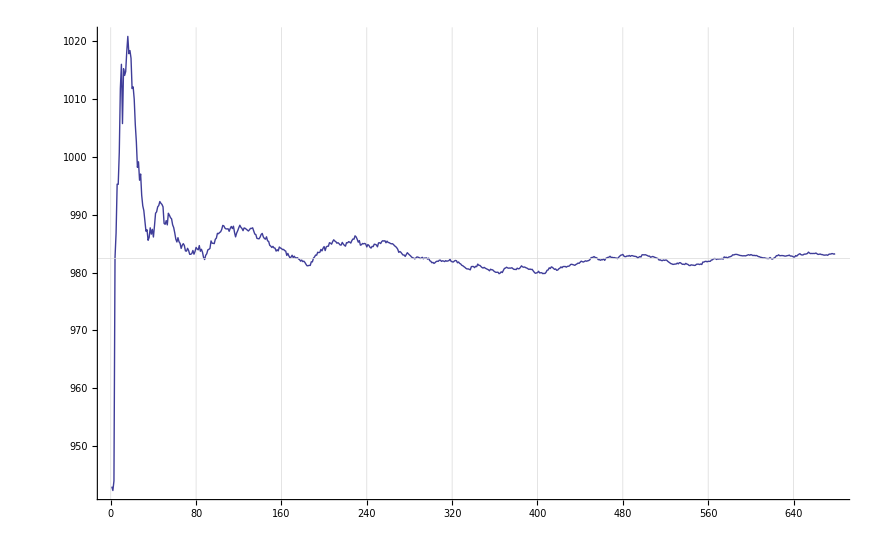

```mathematica
ListPlot[Table[Mean[Take[values,i]],{i,2,Length[values]}],Joined->True,GridLines->{Automatic,{{lim, {Thick,Red}}}}]
```

```mathematica
N[Log[2 3]+Log[2 5]+Log[2 7]+Log[2 11]]
```

9.82444

```mathematica
N[Log[3]+Log[5]+Log[7]+Log[11]]
```

7.05186

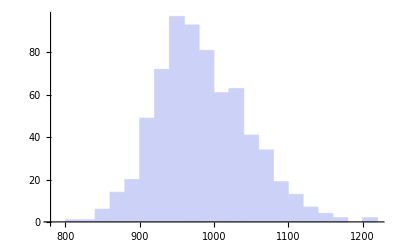

```mathematica
Histogram[values]
```

```mathematica
N[Kurtosis[values]]
```

3.03797

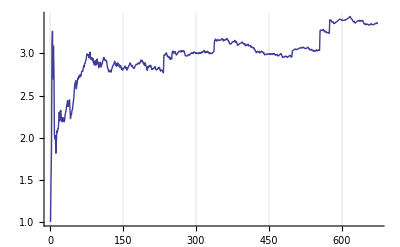

```mathematica
ListPlot[Table[Kurtosis[Take[values,i]],{i,2,Length[values]}],Joined->True,GridLines->{Automatic,{{lim, {Thick,Red}}}}]
```

```mathematica
N[Skewness[values]]
```

0.304203

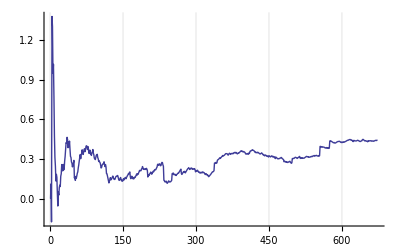

```mathematica
ListPlot[Table[Skewness[Take[values,i]],{i,2,Length[values]}],Joined->True,GridLines->{Automatic,{{lim, {Thick,Red}}}}]
```

```mathematica
values
```

{921,965,941,949,1137,1008,1046,995,1045,1111,1058,893,1129,999,1024,1070,1063,967,1028,992,907,1018,963,905,931,888,1024,910,1027,887,937,965,932,928,996,922,1004,1049,945,1020,933,1068,1081,1001,1029,1002,1024,978,982,971,845,981,1022,949,1099,971,966,978,928,960,931,920,955,1033,940,967,927,1022,1003,962,919,981,1019,956,935,983,994,1024,933,1021,1040,962,972,1046,901,1013,940,904,951,1048,1007,1045,993,999,1107,947,984,979,1059,1007,1069,980,1008,1000,1029,1062,980,947,972,987,990,939,1044,1026,946,1035,864,894,1064,1036,1049,1041,945,962,941,1046,979,969,967,967,1014,1021,986,1002,914,915,974,897,978,982,1027,1052,1012,901,946,968,1046,883,971,885,961,950,1014,944,978,904,1020,952,1092,957,970,953,990,950,970,859,1041,909,930,1003,1038,914,1023,936,976,991,945,959,936,1015,936,995,942,923,933,984,992,980,1100,978,1105,1022,1046,979,1083,970,994,1083,932,1077,1041,845,1112,1009,986,1108,969,949,1077,1052,941,961,929,1005,949,935,983,1086,918,940,951,1119,977,1034,965,949,1083,1048,979,1119,943,892,867,1050,800,1003,1036,970,1002,960,865,1082,949,908,949,1057,976,1087,975,961,905,1155,991,951,1071,1026,967,1001,893,1060,925,976,954,964,991,948,926,949,933,909,838,1026,942,916,922,989,911,1075,1072,925,935,936,925,944,969,944,1027,1035,969,965,936,1004,1021,909,1016,983,994,915,1033,853,951,906,1001,926,1023,1037,1005,971,1046,982,917,1014,965,956,1034,948,1000,998,1057,870,956,966,1034,1020,966,867,1026,901,951,907,953,931,938,922,948,985,955,949,1170,991,977,914,1060,961,1134,910,975,915,920,948,1022,933,946,948,948,918,1079,947,975,910,931,944,984,983,887,1018,1062,932,1117,1106,1006,1034,938,961,992,972,1009,919,932,987,963,1074,939,994,1063,1083,914,954,997,934,957,934,935,1007,946,995,874,885,908,1004,1002,1077,863,992,980,915,1003,965,1068,1125,1002,1132,931,1098,947,906,911,1012,882,999,1072,1026,1071,920,1072,979,988,929,1038,992,1007,1083,1000,959,955,950,1047,1023,1047,958,1069,1062,942,957,1025,1031,952,1011,1005,1035,1130,1024,992,1041,915,967,936,863,994,925,1031,972,1059,861,1135,1033,1021,998,1056,892,986,955,992,952,971,937,1088,1069,1072,1005,1029,843,937,989,1038,962,1041,910,1041,981,947,965,971,958,861,1070,1034,944,1171,987,970,1002,946,945,928,993,879,1017,1018,944,943,948,940,951,846,1008,923,964,1045,944,1013,975,886,906,913,910,952,935,998,999,986,1065,912,1088,978,896,919,995,951,1089,916,950,891,957,1057,958,974,954,993,1078,995,982,943,1036,930,1218,978,1041,997,935,1030,976,989,1102,1005,1083,1010,962,910,1061,936,1029,952,1039,904,1209,922,1016,887,1083,1010,1016,1032,1108,967,1031,996,975,947,948,947,973,957,987,987,969,1027,1028,1019,923,1057,936,921,1018,937,1010,941,909,965,928,962,946,971,988,933,968,969,987,1090,876,914,1047,1055,1065,1141,978,1077,891,983,997,974,962,947,995,1024,993,1035,881,985,949,911,975,1141,926,1104,1070,1044,874,949,996,1066,982,1007,1029,1142,877,922,1002,973,994,974,1041,893,910,1003,1012,924,977,934,966,994,1002,933,1094,1020,984,1040,959,934,1048}

```mathematica
z= Binomial [2 * 3160, 3160]
```

32444190244921375449525053406026907272682306234993552465459504982496116342276252553937060731108974749936394634935314415184777334503602104488596947968124212140080491147999731680509446066143992878895226748409275187362368117059357153916492054714509728688864620311624224670583925791631338421075377510954666558743821153986195288869015960511026239301896555948800499175464712103835625046799714679845007792928694281664496983130462573234518977176872638922286738483090113396479454779416310739151709744123792856935141307438777487628684733230475932239323185963768427370049358287039992872476519806653425144066791724951883992732809138905393738895552536377743358533295361454690801817560713030445346568759457476072057764078340006564869562101252191461620754802462741382343006436398113784275259612450743188894647572910868956918422352141318112901572223863400716522509922058960636607017068396753066241932085168697652190846116133604230420958645877844405070922099631990445229837822337356365355912828281889371390619435197684726552851384925782758013192026109650984377064721933811395187206748528926138125989246331229133331208364814693924696913768604778049158471056711945523445301957485230997379747443260405903862112026480827956787739876314643237823051887914535585124136397318473666923997745352602956793112277943297827060273451496760890749097395629297496808799688578866316065314868024676511732235389935909014541478962496263163766096334740690164753823739729496551260070711555956286892538546265120125835768996752692370684892965843673343004648558649607606091419971372762843656177533047179854584777281406707552949636407167205919501461817414306057664028255518703439343174074261407954147328314844811113236731414263420058511120964028544009169676297478937533715484061094912511704124673882619800254406916695642552127738593869927180190115328393432810476843754144357907071220949304037711865733052891720900621122936092352344677638511536864

```mathematica
Monitor[ListPlot[Table[Map[{n,First[#]}&,FactorInteger[Binomial[2 n, n]]],{n,1,2000}],PlotStyle->Black],n]
```

-Graphics-